# Gradient in cartesian coordinates

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
SetCoordinates[Cartesian[x,y,z]];
```

```mathematica
{CoordinateSystem,Coordinates[],CoordinateRanges[]}
```

{Cartesian,{x,y,z},{-∞<x<∞,-∞<y<∞,-∞<z<∞}}

### Exemple 1

```mathematica
a:=-π;b:=π
```

```mathematica
f[x_,y_]=Sin[x]Sin[y];
```

```mathematica
Plot3D[f[x,y],{x,-a,a},{y,-b,b}]
```

-Graphics3D-

```mathematica
Grad[f[x,y]]//MatrixForm
```

(Cos[x] Sin[y]
Cos[y] Sin[x]
0)

```mathematica
gradf[x_,y_]={Grad[f[x,y]][[1]],Grad[f[x,y]][[2]]};
```

```mathematica
g1:=ContourPlot[f[x,y],{x,-a,a},{y,-a,a},ColorFunction->ColorData["Rainbow"],ContourLabels->True]
```

```mathematica
g2:=VectorPlot[gradf[x,y],{x,-a,a},{y,-b,b}]
```

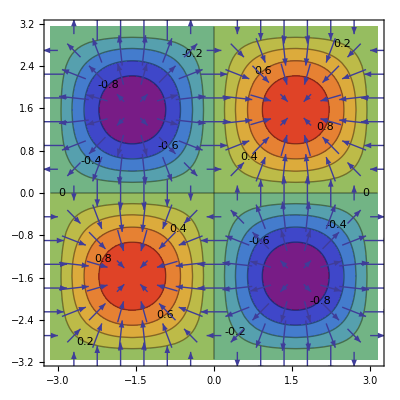

```mathematica
Show[g1,g2]
```

```mathematica
gradf[2,0]//N
```

{0.,0.909297}

```mathematica
Norm[%]
```

0.909297

### Exemple 1

```mathematica
f[x_,y_]=x^3 y^2;
```

```mathematica
u={4,-3,0};
```

```mathematica
gradf[x_,y_]=Grad[f[x,y]]
```

{3 x^2 y^2,2 x^3 y,0}

```mathematica
gradf[-1,2]
```

{12,-4,0}

```mathematica
gradf[-1,2].u
```

60